√(-3 r v+(r+v)^2)

(r+v-√(-3 r v+(r+v)^2))/(3 v)

(r+v+√(-3 r v+(r+v)^2))/(3 v)

-Graphics3D-

r (1-(√(-3 r v+(r+v)^2))/(r+v))-(r+v) (1-(√(-3 r v+(r+v)^2))/(r+v))^2+v (1-(√(-3 r v+(r+v)^2))/(r+v))^3

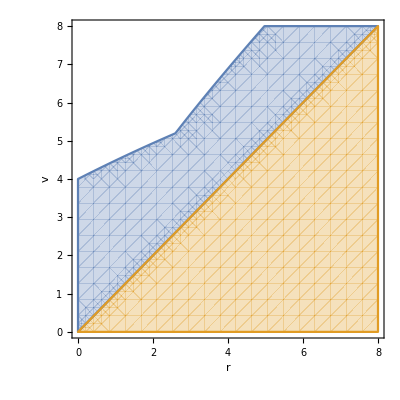

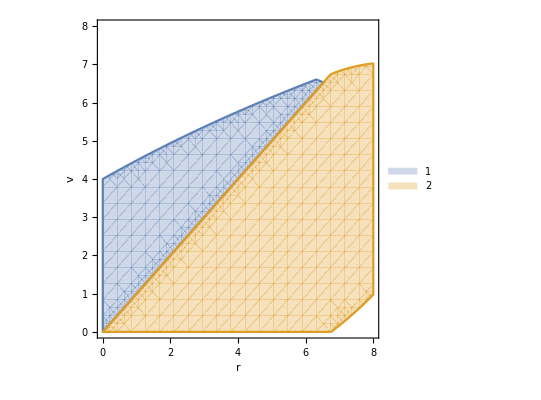

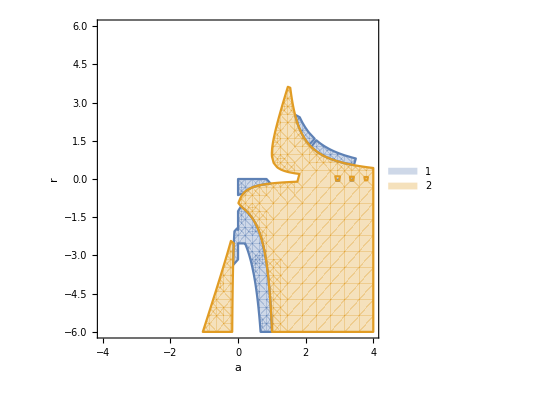

Show[-Graphics-,√(-3 r v+(r+v)^2)]

```mathematica
f[x_]:=v*x^3-(r+v)x^2+r*x
q=Sqrt[(r+v)^2-3*r*v]
t1 = ((r+v)-q)/(3v)
t2 =  ((r+v)+q)/(3v)
Plot3D[f[t],{r,-3,3},{v,-3,3},Mesh->None,PlotStyle->Opacity[0.8],PlotRange->{{-3,3},{-3,3},{0,1}},AxesLabel->{r,v,"f(r,v)"}]
f[t]

g = Graphics[
RegionPlot[{r>v&&(f[t1]<1||-f[t2]<(r/v-1)),r<v&&(f[t1]<r/v||-f[t2]<(1-r/v))}, {v,0,8},{r,0,8},AxesLabel->{"r","v"}]];
p=Graphics[{PointSize[Large],Blue,Point[{2,5}]}];
Show[g,Axes->True]
RegionPlot[{r>v&&(f[t1]<1),r<v&&(f[t1]-f[t2]<1)}, {v,0,8},{r,0,8},FrameLabel->{"r","v"},Axes->True, PlotLegends->Automatic,LabelStyle-> Medium]
RegionPlot[{(-r*a(1-a)-a>(r+1)^2/(4r)&&2a>-2*r*a(1-a)-2a),((-r*a*(1-a)-a)<((r+1)^2/(4r))&&(2*a)>((r+1)^2/(2r)))},{a,-4,4},{r,-6,6},Axes->True, PlotLegends->Automatic, FrameLabel->{"a","r"},LabelStyle-> Medium]
Show[p,q]
```

```mathematica
MaxValue[{-r*a*(1-a)-a<(r+1)^2/(4r)&&2*a>(r+1)^2/(2r)},{r,a}]
MaxValue[{r,(-r*a*(1-a)-a)<((r+1)^2/(4r))&&(2*a)>((r+1)^2/(2r))},r]
```

MaxValue[{-a-(1-a) a r<(1+r)^2/(4 r)&&2 a>(1+r)^2/(2 r)},{r,a}]

Piecewise[{{-1+2 a-2 √((-1+a) a), a<1/7 (5-4 √2)}, {-1+2 a+2 √((-1+a) a), 1<a≤1/7 (5+4 √2)}, {(1+2 a-2 √2 √(a^2/((-1-4 a+4 a^2)^2))-8 √2 a √(a^2/((-1-4 a+4 a^2)^2))+8 √2 a^2 √(a^2/((-1-4 a+4 a^2)^2)))/(-1-4 a+4 a^2), a>1/7 (5+4 √2)||0<a≤1}, {-∞, True}}]